```mathematica
n[r_,nH_,nL_,Ai_,AWS_]:=nH/(1+Exp[(r-Rws[Ai,nH])/AWS])+nL/(1+Exp[(-(r-Rws[Ai,nH]))/AWS]);
d2n[r_,nH_,nL_,Ai_,AWS_]:=(2 (nH-nL) Csch[(r-Rws[Ai,nH])/AWS]^3 Sinh[(r-Rws[Ai,nH])/(2 AWS)]^4)/AWS^2;
dn[r_,nH_,nL_,Ai_,AWS_]:=((-nH+nL) Sech[(r-Rws[Ai,nH])/(2 AWS)]^2)/(4 AWS);
Rws[Ai_,nH_]:=Ri[Ai,nH](1-π^2/3(aws/Ri[Ai,nH])^2);
Ri[Ai_,nH_]:=((3 Ai)/(4 π nH))^(1/3);
aws=α+ β δnH^2;

(*α= 0.53;
 β= 0.35;*)
```

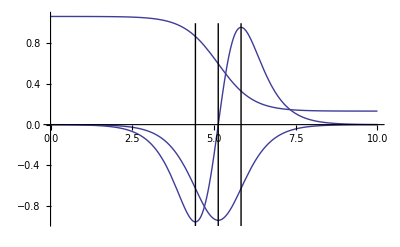

```mathematica
Show[Plot[{n[r,0.16,0.02,100,aws]/0.15,dn[r,0.16,0.02,100,aws]/0.07,d2n[r,0.16,0.02,100,aws]/0.05}//.α-> 0.53//.δnH->0.01 //.β-> 0.02,{r,0,10}],Graphics[Line[{{(aws  ArcCosh[2]+Rws[100,0.16])//.α-> 0.53//.δnH->0.01 //.β-> 0.02,-1},{(aws  ArcCosh[2]+Rws[100,0.16])//.α-> 0.53//.δnH->0.01 //.β-> 0.02,1}}]],Graphics[Line[{{(-aws  ArcCosh[2]+Rws[100,0.16])//.α-> 0.53//.δnH->0.01 //.β-> 0.02,-1},{(-aws  ArcCosh[2]+Rws[100,0.16])//.α-> 0.53//.δnH->0.01 //.β-> 0.02,1}}]],Graphics[Line[{{Rws[100,0.16]//.α-> 0.53//.δnH->0.01 //.β-> 0.02,-1},{Rws[100,0.16]//.α-> 0.53//.δnH->0.01 //.β-> 0.02,1}}]]]
```

```mathematica
aws  ArcCosh[2]
```

(α+β δnH^2) ArcCosh[2]

#### Interpolated energy density :

```mathematica
slope=(EnH-EnL)/(-2 aws  ArcCosh[2]);
En[r_]:=EnH+slope*r;
FullSimplify[Integrate[4 π r^2En[r],{r,Rws -aws  ArcCosh[2],Rws+aws  ArcCosh[2]}]]
```

4/3 π (6 aws EnH Rws^2 ArcCosh[2]+2 aws^3 EnH ArcCosh[2]^3-3 (EnH-EnL) Rws (Rws^2+aws^2 ArcCosh[2]^2))

```mathematica
Collect[Apart[FullSimplify[1/(4 π Rws^2)4/3 π (6 aws EnH Rws^2 ArcCosh[2]+2 aws^3 EnH ArcCosh[2]^3-3 (EnH-EnL) Rws (Rws^2+aws^2 ArcCosh[2]^2))]],{(EnH-EnL),EnH},FullSimplify]
```

(EnH-EnL) (-Rws+(aws^2 ArcCos[2]^2)/Rws)+EnH (2 aws ArcCosh[2]+(2 aws^3 ArcCosh[2]^3)/(3 Rws^2))